```mathematica
$ImportFormats;
scatterdata=Import["C:\\Users\\shahn\\OneDrive\\Desktop\\data sheet.csv"];
data1 = Transpose[{scatterdata[[2;;4,3]], scatterdata[[2;;4,22]]}];
data2 = Transpose[{scatterdata[[5;;8,3]], scatterdata[[ 5;;8,22]]}];
data3 = Transpose[{scatterdata[[9;;13,3]], scatterdata[[9;;13,22]]}];
data4 = Transpose[{scatterdata[[14;;17,3]], scatterdata[[14;;17,22]]}];
data5 = Transpose[{scatterdata[[18;;24,3]], scatterdata[[18;;24,22]]}];
data6 = Transpose[{scatterdata[[25;;28,3]], scatterdata[[25;;28,22]]}];
data7 = Transpose[{scatterdata[[29;;33,3]], scatterdata[[29;;33,22]]}];
data8 = Transpose[{scatterdata[[34;;39,3]], scatterdata[[34;;39,22]]}];
data9 = Transpose[{scatterdata[[40;;44,3]], scatterdata[[40;;44,22]]}];
data10 = Transpose[{scatterdata[[45;;46,3]], scatterdata[[45;;46,22]]}];
data11= Transpose[{scatterdata[[47;;48,3]], scatterdata[[47;;48,22]]}];
```

```mathematica
(*making list of sigma values for each Q^2*)
sigma1= scatterdata[[2;;4,22]];
sigma2= scatterdata[[5;;8,22]];
sigma3= scatterdata[[9;;13,22]];
sigma4= scatterdata[[14;;17,22]];
sigma5= scatterdata[[18;;24,22]];
sigma6= scatterdata[[25;;28,22]];
sigma7= scatterdata[[29;;33,22]];
sigma8= scatterdata[[34;;39,22]];
sigma9= scatterdata[[40;;44,22]];
sigma10= scatterdata[[45;;46,22]];
sigma11= scatterdata[[47;;48,22]];
```

```mathematica
(*making list of epsilon values for each Q^2*)
eps1=scatterdata[[2;;4,3]];
eps2= scatterdata[[5;;8,3]];
eps3= scatterdata[[9;;13,3]];
eps4= scatterdata[[14;;17,3]];
eps5= scatterdata[[18;;24,3]];
eps6= scatterdata[[25;;28,3]];
eps7= scatterdata[[29;;33,3]];
eps8= scatterdata[[34;;39,3]];
eps9= scatterdata[[40;;44,3]];
eps10= scatterdata[[45;;46,3]];
eps11= scatterdata[[47;;48,3]];
```

```mathematica
(*making list of statistical error values for each Q^2*)
stat1 = scatterdata[[2;;4,12]];
stat2= scatterdata[[5;;8,12]];
stat3= scatterdata[[9;;13,12]];
stat4= scatterdata[[14;;17,12]];
stat5= scatterdata[[18;;24,12]];
stat6= scatterdata[[25;;28,12]];
stat7= scatterdata[[29;;33,12]];
stat8= scatterdata[[34;;39,12]];
stat9= scatterdata[[40;;44,12]];
stat10= scatterdata[[45;;46,12]];
stat11= scatterdata[[47;;48,12]];
```

```mathematica
(*making list of systamatic error values for each Q^2*)
syst1 = scatterdata[[2;;4,13]];
syst2= scatterdata[[5;;8,13]];
syst3= scatterdata[[9;;13,13]];
syst4= scatterdata[[14;;17,13]];
syst5= scatterdata[[18;;24,13]];
syst6= scatterdata[[25;;28,13]];
syst7= scatterdata[[29;;33,13]];
syst8= scatterdata[[34;;39,13]];
syst9= scatterdata[[40;;44,13]];
syst10= scatterdata[[45;;46,13]];
syst11= scatterdata[[47;;48,13]];
```

```mathematica
(*writing the sigma value with its corresponding error for each Q^2. The quadrature sum of systamatic and statistical errors are taken here*)
sigmaerror1 = Table[Around[sigma1[[i]],Sqrt[(stat1[[i]]*sigma1[[i]]/100)^2+(syst1[[i]]*sigma1[[i]]/100)^2]],{i,1,Length[sigma1]}];
sigmaerror2= Table[Around[sigma2[[i]], Sqrt[(stat2[[i]]*sigma2[[i]]/100)^2+(syst2[[i]]*sigma2[[i]]/100)^2]],{i,1,Length[sigma2]}];
sigmaerror3 = Table[Around[sigma3[[i]],Sqrt[(stat3[[i]]*sigma3[[i]]/100)^2+(syst3[[i]]*sigma3[[i]]/100)^2]],{i,1,Length[sigma3]}];
sigmaerror4 = Table[Around[sigma4[[i]], Sqrt[(stat4[[i]]*sigma4[[i]]/100)^2+(syst4[[i]]*sigma4[[i]]/100)^2]],{i,1,Length[sigma4]}];
sigmaerror5 = Table[Around[sigma5[[i]], Sqrt[(stat5[[i]]*sigma5[[i]]/100)^2+(syst5[[i]]*sigma5[[i]]/100)^2]],{i,1,Length[sigma5]}];
sigmaerror6 = Table[Around[sigma6[[i]], Sqrt[(stat6[[i]]*sigma6[[i]]/100)^2+(syst6[[i]]*sigma6[[i]]/100)^2]],{i,1,Length[sigma6]}];
sigmaerror7 = Table[Around[sigma7[[i]], Sqrt[(stat7[[i]]*sigma7[[i]]/100)^2+(syst7[[i]]*sigma7[[i]]/100)^2]],{i,1,Length[sigma7]}];
sigmaerror8 = Table[Around[sigma8[[i]], Sqrt[(stat8[[i]]*sigma8[[i]]/100)^2+(syst8[[i]]*sigma8[[i]]/100)^2]],{i,1,Length[sigma8]}];
sigmaerror9 = Table[Around[sigma9[[i]], Sqrt[(stat9[[i]]*sigma9[[i]]/100)^2+(syst9[[i]]*sigma9[[i]]/100)^2]],{i,1,Length[sigma9]}];
sigmaerror10 = Table[Around[sigma10[[i]],Sqrt[(stat10[[i]]*sigma10[[i]]/100)^2+(syst10[[i]]*sigma10[[i]]/100)^2]],{i,1,Length[sigma10]}];
sigmaerror11= Table[Around[sigma11[[i]], Sqrt[(stat11[[i]]*sigma11[[i]]/100)^2+(syst11[[i]]*sigma11[[i]]/100)^2]],{i,1,Length[sigma11]}];
```

```mathematica
(*Linear fit of the graph*)
line1  = Fit[data1,{1,x},x];
line2  = Fit[data2,{1,x},x];
line3  = Fit[data3,{1,x},x];
line4  = Fit[data4,{1,x},x];
line5  = Fit[data5,{1,x},x];
line6  = Fit[data6,{1,x},x];
line7  = Fit[data7,{1,x},x];
line8  = Fit[data8,{1,x},x];
line9  = Fit[data9,{1,x},x];
line10  = Fit[data10,{1,x},x];
line11  = Fit[data11,{1,x},x];
```

```mathematica
line1er = Fit[Transpose[{eps1,sigmaerror1}], {1,x},x]
line2er = Fit[Transpose[{eps2,sigmaerror2}], {1,x},x]
line3er = Fit[Transpose[{eps3,sigmaerror3}], {1,x},x]
line4er = Fit[Transpose[{eps4,sigmaerror4}], {1,x},x]
line5er = Fit[Transpose[{eps5,sigmaerror5}], {1,x},x]
line6er = Fit[Transpose[{eps6,sigmaerror6}], {1,x},x]
line7er = Fit[Transpose[{eps7,sigmaerror7}], {1,x},x]
line8er = Fit[Transpose[{eps8,sigmaerror8}], {1,x},x]
line9er = Fit[Transpose[{eps9,sigmaerror9}], {1,x},x]
line10er = Fit[Transpose[{eps10,sigmaerror10}], {1,x},x]
line11er = Fit[Transpose[{eps11,sigmaerror11}], {1,x},x]
```

x (0.0290.005)+(0.0700.004)

x (0.00570.0007)+(0.03060.0004)

x (0.00400.0018)+(0.02340.0014)

x (0.00190.0010)+(0.01500.0007)

x (0.001550.00030)+(0.015160.00020)

x (0.00150.0006)+(0.00950.0005)

x (0.000600.00022)+(0.008420.00014)

x (0.000270.00012)+(0.005060.00008)

x (0.000090.00008)+(0.002860.00005)

x (0.000070.00006)+(0.0016870.000035)

x (0.000110.00006)+(0.0010720.000034)

```mathematica
Show[ListPlot[Transpose[{eps1,sigmaerror1}], PlotTheme-> "Monochrome"],Plot[line1,{x,0,1.1}] ,BaseStyle-> {FontFamily-> "Times New Roman"},Frame-> True,FrameLabel-> {"ϵ", "σ_R"},PlotLabel-> "Q^2 = 1 GeV^2",PlotRange-> {{0.65,1.05},{.086,.101}},Axes-> False]
```

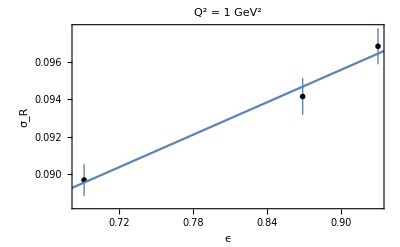

```mathematica
Show[ListPlot[Transpose[{eps1,sigmaerror1}], PlotTheme-> "Monochrome"],Plot[line1,{x,0,1}] ,BaseStyle-> {FontFamily-> "Times New Roman"},Frame-> True,FrameLabel-> {"ϵ", "σ_R"},PlotLabel-> "Q^2 = 1 GeV^2"]
```

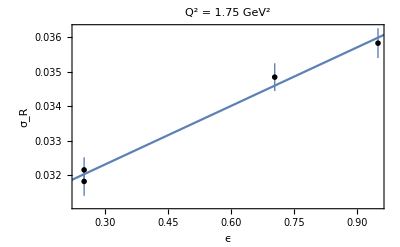

```mathematica
Show[ListPlot[Transpose[{eps2,sigmaerror2}], PlotTheme-> "Monochrome"],Plot[line2,{x,0,1}] ,BaseStyle-> {FontFamily-> "Times New Roman"},Frame-> True,FrameLabel-> {"ϵ", "σ_R"},PlotLabel-> "Q^2 = 1.75 GeV^2"]
```

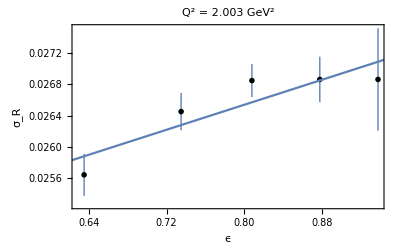

```mathematica
Show[ListPlot[Transpose[{eps3,sigmaerror3}], PlotTheme-> "Monochrome"],Plot[line3,{x,0,1}] ,BaseStyle-> {FontFamily-> "Times New Roman"},Frame-> True,FrameLabel-> {"ϵ", "σ_R"},PlotLabel-> "Q^2 = 2.003 GeV^2"]
```

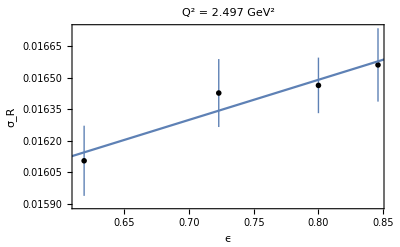

```mathematica
Show[ListPlot[Transpose[{eps4,sigmaerror4}], PlotTheme-> "Monochrome"],Plot[line4,{x,0,1}] ,BaseStyle-> {FontFamily-> "Times New Roman"},Frame-> True,FrameLabel-> {"ϵ", "σ_R"},PlotLabel-> "Q^2 = 2.497 GeV^2"]
```

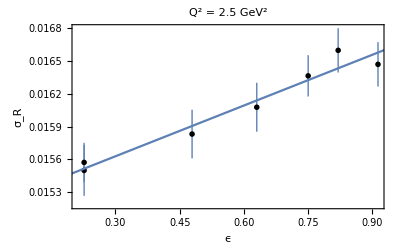

```mathematica
Show[ListPlot[Transpose[{eps5,sigmaerror5}], PlotTheme-> "Monochrome"],Plot[line5,{x,0,1}] ,BaseStyle-> {FontFamily-> "Times New Roman"},Frame-> True,FrameLabel-> {"ϵ", "σ_R"},PlotLabel-> "Q^2 = 2.5 GeV^2"]
```

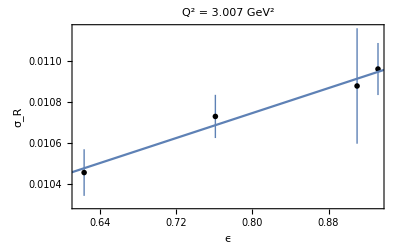

```mathematica
Show[ListPlot[Transpose[{eps6,sigmaerror6}], PlotTheme-> "Monochrome"],Plot[line6,{x,0,1}] ,BaseStyle-> {FontFamily-> "Times New Roman"},Frame-> True,FrameLabel-> {"ϵ", "σ_R"},PlotLabel-> "Q^2 = 3.007 GeV^2"]
```

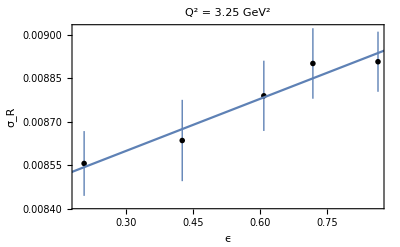

```mathematica
Show[ListPlot[Transpose[{eps7,sigmaerror7}], PlotTheme-> "Monochrome"],Plot[line7,{x,0,1}] ,BaseStyle-> {FontFamily-> "Times New Roman"},Frame-> True,FrameLabel-> {"ϵ", "σ_R"},PlotLabel-> "Q^2 = 3.25 GeV^2"]
```

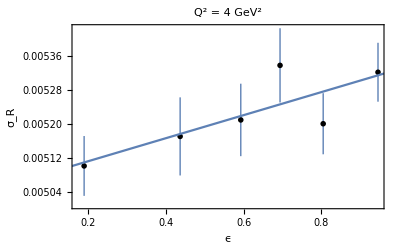

```mathematica
Show[ListPlot[Transpose[{eps8,sigmaerror8}], PlotTheme-> "Monochrome"],Plot[line8,{x,0,1}] ,BaseStyle-> {FontFamily-> "Times New Roman"},Frame-> True,FrameLabel-> {"ϵ", "σ_R"},PlotLabel-> "Q^2 = 4 GeV^2"]
```

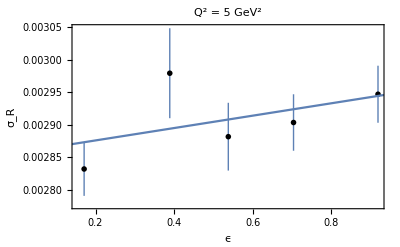

```mathematica
Show[ListPlot[Transpose[{eps9,sigmaerror9}], PlotTheme-> "Monochrome"],Plot[line9,{x,0,1}] ,BaseStyle-> {FontFamily-> "Times New Roman"},Frame-> True,FrameLabel-> {"ϵ", "σ_R"},PlotLabel-> "Q^2 = 5 GeV^2"]
```

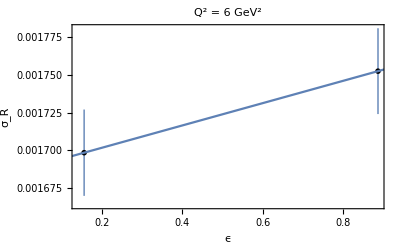

```mathematica
Show[ListPlot[Transpose[{eps10,sigmaerror10}], PlotTheme-> "Monochrome"],Plot[line10,{x,0,1}] ,BaseStyle-> {FontFamily-> "Times New Roman"},Frame-> True,FrameLabel-> {"ϵ", "σ_R"},PlotLabel-> "Q^2 = 6 GeV^2"]
```

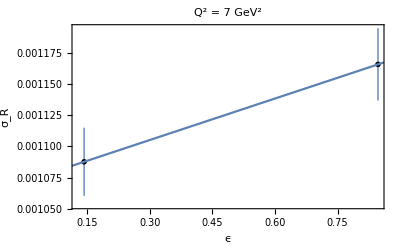

```mathematica
Show[ListPlot[Transpose[{eps11,sigmaerror11}], PlotTheme-> "Monochrome"],Plot[line11,{x,0,1}] ,BaseStyle-> {FontFamily-> "Times New Roman"},Frame-> True,FrameLabel-> {"ϵ", "σ_R"},PlotLabel-> "Q^2 = 7 GeV^2"]
```

```mathematica
`
```